```mathematica
<<PrettyTheme`
```

```mathematica
nNeurons=40;
h=0.5;a=0.1;
excStr=1.0;inhStr=2.5;
```

```mathematica
MultiNeuronHomoWithinGroupTheoryPade[
1.0,h,a,
bivariateWeightMatrix[nNeurons,excStr,inhStr],
Partition[Range[1,nNeurons],nNeurons/4],
generateInitial[h,nNeurons,1]
]
```

{1.55,1.5,1.55,1.5}

{0.0760278,0.0644885,0.088957,0.0752051}

$Aborted

```mathematica
pred1[exc_]:=With[{nNeurons=40,τ=1,h=0.5,a=0.1,inh=3.0},
MultiNeuronHomoTheoryMomentsBetaX[
τ,h,a,
bivariateWeightMatrix[nNeurons,exc,inh],
2,
Partition[Range[1,nNeurons],nNeurons/4],
generateInitial[h,nNeurons,1]
]
];
```

```mathematica
excVarList[[51]]
```

2.

```mathematica
needToChange=51;
```

```mathematica
simulationForHigherMoments[[needToChange]]=MultiNeuronSimulation[1.0,h,a,bivariateWeightMatrix[nNeurons,excVarList[[needToChange]],3.0],True,300000];
```

Simulation progress:    %    ETA:

```mathematica
Export[NotebookDirectory[]<>"data_HigerMomentsMulti//simulationForHigherMoments_"<>ToString[needToChange]<>".dat",simulationForHigherMoments[[needToChange]]]
```

/Users/luyan/Dropbox/Research/InhibitionDEs/data_HigerMomentsMulti//simulationForHigherMoments_51.dat

```mathematica
splitedData[[needToChange]]=splitBistableData[simulationForHigherMoments[[needToChange]],-6.0,-6.0,Mean[#[[;;nNeurons/4]]]&,50];
momentsBetaMono[[needToChange]]=computeMomentsOfBetaFromSection[simulationForHigherMoments[[needToChange]]];
momentsBetaUp[[needToChange]]=computeMomentsOfBetaFromMultipleSection[splitedData[[needToChange]]["up"]];
momentsBetaDown[[needToChange]]=computeMomentsOfBetaFromMultipleSection[splitedData[[needToChange]]["down"]];
momentsXMono[[needToChange]]=computeMomentsOfXFromSection[simulationForHigherMoments[[needToChange]],1.];
momentsXUp[[needToChange]]=computeMomentsOfXFromMultipleSection[splitedData[[needToChange]]["up"],1.];
momentsXDown[[needToChange]]=computeMomentsOfXFromMultipleSection[splitedData[[needToChange]]["down"],1.];
```

```mathematica
excVarList=Prepend[Range[0.04,2.0,0.04],0.01];
```

```mathematica
multiHigherMomentsPade1=ParallelTable[Print[exc];pred1[exc],{exc,excVarList}];
```

```mathematica
read[multiHigherMomentsPade1]
```

```mathematica
simulationForHigherMoments=Table[
Print[exc];MultiNeuronSimulation[1.0,h,a,bivariateWeightMatrix[nNeurons,exc,3.0],True,300000],
{exc,excVarList}];
```

```mathematica
(*Table[Export[NotebookDirectory[]<>"data_HigerMomentsMulti//simulationForHigherMoments_"<>ToString[i]<>".dat",simulationForHigherMoments[[i]]],{i,1,Length[simulationForHigherMoments]}]*)
```

```mathematica
processDataFile[entry_]:={entry[[1]],entry[[2]],ToExpression[StringJoin[entry[[3;;]]]]};
simulationForHigherMoments=Table[PrintTemporary[i];(ParallelMap[processDataFile,Import[NotebookDirectory[]<>"data_HigerMomentsMulti//simulationForHigherMoments_"<>ToString[i]<>".dat"]]),{i,1,Length[excVarList]}];
```

```mathematica
splitBistableData[simData_,upThres_,downThres_,measureFunc_,minEventCount_:1]:=Module[{
upStates={},downStates={},
upIds={},downIds={},ids={},
i,measure,curState,prevState=0,states={}
},
For[i=1,i≤Length[simData],i++,

measure=measureFunc[simData[[i,3]]];
curState=If[measure≥upThres,1,If[measure≤downThres,-1,0]];

If[curState==prevState,
AppendTo[states,simData[[i]]];
AppendTo[ids,i];
,
If[Length[states]≥minEventCount,
If[prevState==1,
AppendTo[upStates,states];
AppendTo[upIds,ids];
,
If[prevState==-1,
AppendTo[downStates,states];
AppendTo[downIds,ids];]
]
];
states={simData[[i]]};
ids={i};
prevState=curState;
];

];
If[Length[states]≥minEventCount,
If[prevState==1,
AppendTo[upStates,states];
AppendTo[upIds,ids];
,
If[prevState==-1,
AppendTo[downStates,states];
AppendTo[downIds,ids];]
]
];


<|"upIds"->upIds,"up"->upStates,"downIds"->downIds,"down"->downStates|>
];

computeMomentsOfBetaFromSection[section_]:=Module[{n=Length[section[[1,3]]]},
Table[If[Length[#]≤2,0.,(Length[#]-1)/(#[[-1,1]]-#[[1,1]])]&@Select[section,#[[2]]==i&],{i,1,n}]
];

computeMomentsOfBetaFromMultipleSection[sections_]:=
Mean[computeMomentsOfBetaFromSection[#]&/@sections];

computeMomentsOfXFromSection[section_,τ_]:=Module[{ts,xs,dt},
ts=section[[All,1]];
xs=section[[All,3]];
dt=Differences[ts];
Quiet@Table[
Total[xs[[;;-2]]^k*τ/k*(1-Exp[-dt*k/τ])]/(ts[[-1]]-ts[[1]]),
{k,1,2}]
];

computeMomentsOfXFromMultipleSection[sections_,τ_]:=
Mean[computeMomentsOfXFromSection[#,τ]&/@sections];
```

```mathematica
splitedData=ParallelTable[splitBistableData[dataset,-6.0,-6.0,Mean[#[[;;nNeurons/4]]]&,50],{dataset,simulationForHigherMoments}];
```

```mathematica
momentsBetaMono=ParallelTable[computeMomentsOfBetaFromSection[dataset],{dataset,simulationForHigherMoments}];
```

```mathematica
momentsBetaUp=ParallelTable[computeMomentsOfBetaFromMultipleSection[dataset["up"]],{dataset,splitedData}];
```

```mathematica
momentsBetaDown=ParallelTable[computeMomentsOfBetaFromMultipleSection[dataset["down"]],{dataset,splitedData}];
```

```mathematica
momentsXMono=ParallelTable[computeMomentsOfXFromSection[dataset,1.],{dataset,simulationForHigherMoments}];
```

```mathematica
momentsXUp=ParallelTable[computeMomentsOfXFromMultipleSection[dataset["up"],1.],{dataset,splitedData}];
```

```mathematica
momentsXDown=ParallelTable[computeMomentsOfXFromMultipleSection[dataset["down"],1.],{dataset,splitedData}];
```

```mathematica
save[momentsBetaMono];
save[momentsBetaUp];
save[momentsBetaDown];
save[momentsXMono];
save[momentsXUp];
save[momentsXDown];
```

```mathematica
predUnstable[exc_]:=With[{nNeurons=40,τ=1,h=0.5,a=0.1,inh=3.0},
MultiNeuronHomoTheoryMomentsBetaX[
τ,h,a,
bivariateWeightMatrix[nNeurons,exc,inh],
2,
Partition[Range[1,nNeurons],nNeurons/2],
generateInitial[h,nNeurons,0]
]
];
```

```mathematica
unstableMoments=ParallelTable[Print[exc];predUnstable[exc],{exc,excVarList[[33;;]]}];
```

1.28

1.36

1.44

1.52

1.56

1.6

1.64

1.68

1.4

1.32

1.72

1.76

1.8

1.84

1.88

1.48

1.92

1.96

2.

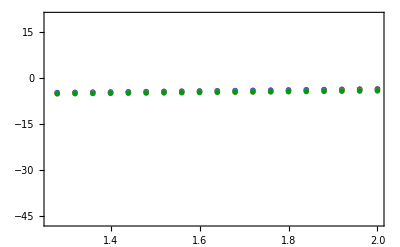

```mathematica
ListPlot[
Join@@{
Thread[{excVarList[[33;;]],#}]&/@Join[
{
unstableMoments[[All,-1,21,2,1]],
unstableMoments[[All,-1,31,2,1]],
unstableMoments[[All,-1,1,2,1]],
unstableMoments[[All,-1,11,2,1]]
}
]
},
PlotRange->{-47,20}
]
```

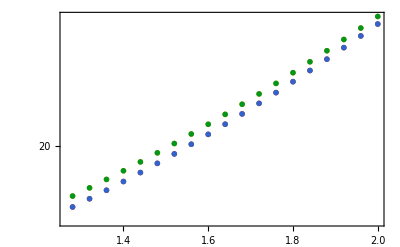

```mathematica
g1=ListLogPlot[
Join@@{
Thread[{excVarList[[33;;]],#}]&/@Join[
{
unstableMoments[[All,-1,21,2,2]]-unstableMoments[[All,-1,21,2,1]]^2,
unstableMoments[[All,-1,31,2,2]]-unstableMoments[[All,-1,31,2,1]]^2,
unstableMoments[[All,-1,1,2,2]]-unstableMoments[[All,-1,1,2,1]]^2,
unstableMoments[[All,-1,11,2,2]]-unstableMoments[[All,-1,11,2,1]]^2
}
]
}
]
```

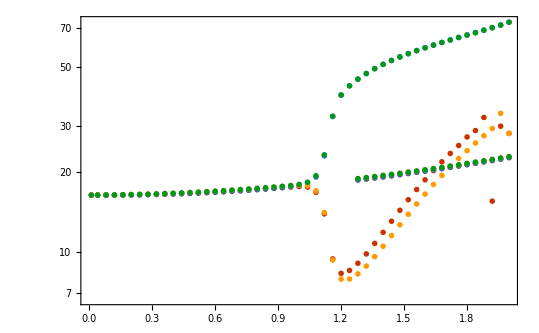

```mathematica
Show[g2,g1]
```

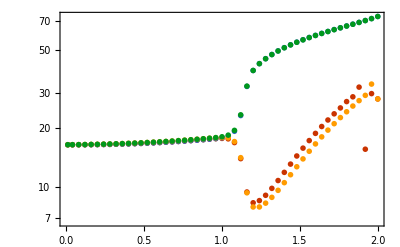

```mathematica
g2=ListLogPlot[
Join@@{
Thread[{excVarList,#}]&/@Join[
{
multiHigherMomentsPade1[[All,-1,21,2,2]]-multiHigherMomentsPade1[[All,-1,21,2,1]]^2,
multiHigherMomentsPade1[[All,-1,31,2,2]]-multiHigherMomentsPade1[[All,-1,31,2,1]]^2,
multiHigherMomentsPade1[[All,-1,1,2,2]]-multiHigherMomentsPade1[[All,-1,1,2,1]]^2,
multiHigherMomentsPade1[[All,-1,11,2,2]]-multiHigherMomentsPade1[[All,-1,11,2,1]]^2
}
]
}
]
```